## Complexes

Some useful functions

MeshCellStyle->{{1,All}→Red,{0,All}→Black}

MeshRegion

guide/MeshRegions

### T^3=S^1×S^1×S^1

BlockMap
ArrayFilter

https://math.stackexchange.com/questions/2017079/uniform-random-points-on-a-torus
https://web.maths.unsw.edu.au/~rsw/Torus/index.php

Mapping:
	circle x_1=(r_1,(e_1,θ_1,e_2))
	circle +(r_2,(x_1,θ_2,e_3)) ⟶x_2
	circle +(r_3,(x_2,θ_3,e_4))⟶x_3

```mathematica
(*<<Colors.wl*)
(*rainbow=d3ColorFun["rainbow"];*)
```

Here’s an iconized version of the “rainbow” function

```mathematica
Iconize[rainbow]
```

```mathematica
rainbow=
```

GENERAL IDEAS
The big picture with this project is to take a parameterization of a 4d torus and manipulate it so it is easier to visualize.

To make the torus we need a parameterization. The domain of the parameterization is D=[0,1]×[0,1]×[0,1], a unit cube.
A number in each interval corresponds to a choice of one "angle", so choosing 3 angles give a point on the torus.
By choosing just the points {(x,y,0)∈D | z = k} we would get a family of regular toruses for different values of k.

For notation, say we have a function F:D ⟶ T^3⊂ℝ^4. Also we'll have another function P:ℝ^4⟶ℝ^3 which will project the torus back to 3-space.
We'll set up some tools to make P dependant on time so we can explore a continuous family of different projections.

The function "torus" computes the function F in a way that lets you choose the radii whenever you want.

```mathematica
ClearAll[torus];
torus[t_]:=Block[{e,d,v,n},
	n=Length[t]+1;
	e[k_]:=UnitVector[n,k];
	d[0]=e[1];
	d[k_]:=Cos[2 π t⟦k⟧]d[k-1]+Sin[2 π t⟦k⟧]e[k+1];
	Transpose[d/@Range[n-1]]];
(* usage: choose three radii {r1, r2, r3} and compute
	torus[{angle1, angle2, angle3}] . {r1, r2, r3}
	This gives a point in R^4 obtained by:
	choosing a direction d[1] in the e1/e2 plane and going a distance r1 to get a point x1.
	choose a direction d[2] obtained by rotating d[1] toward e3 by angle2, and setting x2 = x1 + r2 d2.
	choose a third direction d[3] by rotating d[2] toward e4 by angle3 and setting x3 = x2 + r3 d3.
	return x3.
	The code is structured so that giving more / fewer angles results in a mapping to higher / lower dimensional torii. *)
```

```mathematica
torus[{0.2,0.3,0.8}]//MatrixForm
```

(0.309017 | -0.0954915 | -0.0295085
0.951057 | -0.293893 | -0.0908178
0. | 0.951057 | 0.293893
0. | 0. | -0.951057)

```mathematica
(* test if a cell is axis aligned *)
isAxisAligned[h_[ind_List]]:=!AnyTrue[Apply[ManhattanDistance]/@Subsets[getidx⟦ind⟧,{2}],GreaterThan[Length[ind]-1]];
(* only works after getidx table is defined *)
```

this setup is part of making the projection P be time-dependant.

```mathematica
(* Rotation Matrices *)
ev[n_,k_]:=UnitVector[n,k];
(* used for rotation sliders later - can be any rotation matrix *)
rotator[t_]:=RotationMatrix[t,{Normalize@{Sqrt[3]/2,-0.5,1,1},Normalize@{0,0.006,0,1}}];
r4[t_]:=Dot[
	RotationMatrix[t π/2,{ev[4,1],ev[4,2]}],
	RotationMatrix[t π/3,{ev[4,2],ev[4,3]}],
	RotationMatrix[t 0.6π,{ev[4,3],ev[4,4]}],
	RotationMatrix[t 0.4π, {ev[4,4],ev[4,1]}]
	];
```

Cross-section idea:
	Goal is to be able to say "I want to take a plane H in D and think about what P(F(H)) looks like."
	This amounts to taking a cross-section of D and seeing what kind of torus shape it makes in ℝ^4. But we
	can only look at it after applying the projection P.
	
	To achieve this I decided to use a few functions to assign a number to each cell of the eventual mesh
	based on where in D the point came from.
	
	The function vf should take a set of points in D and return a number between 0 and 1. It is used for color assignment.
	I use it to "rank" points based on their third angle by looking at the component in the direction of {0,0,1}
	which corresponds to angle3 for F.
	
	The function g takes any real number and assigns an opacity. The idea behind using the vf function with g is to make points nearby
	the cross-section be more opaque while points farther from the cross-section should be more transparent. So the tr parameter
	affects the offset of the cross-section while the settings for vf control the orientation of the cross section.
	To make far-away points less visible I used a BlackmannWindow centered at tr.

```mathematica
ClearAll[g,getColor,styfilter,vf];

(* typical values of tr: 0 if there are bugs with other things, otherwise anything in [0,1] *)
(* typical values of w: 0.2, 0.8, 1, 1.5, 2, 3 *)

g[x_,{tr_,w_}]:=Block[{h,center=tr,width=w},
	h[t_]:=Mod[t,1,center-1/2]; (* <-- magic to make g ALWAYS have period 1 and do centering correctly *)
	
	(* use this line to experiment with more aggressive opacity-reduction. Decrease tolerance to allow the first window more influence *)
	tolerance = 3; (* should probably be at least 1 *)
	(* Chop[BlackmanWindow[(h[x]-center)/width]* DirichletWindow[tolerance(h[x]-center)/w]]/.{0->None} *)
	
	(* use this line instead for more gradual transparency transitions *)
	Chop[BlackmanWindow[(h[x]-center)/width]]
	];
g[x_,alpha_]:=alpha;
g[x_]:=1;

(* redefine this at any time to change "direction" of coloring *)
vf[pts_]:=Mod[Mean[pts.Normalize[{0,0,1}]],1]

getColor[ind_List,pars_:None]:=Block[{pts,val,helper},
	pts=Extract[pttable,getidx⟦ind⟧];
	val=vf[pts];
	helper[None]=None;
	helper[opac_]:=Directive[Opacity[opac],rainbow[val]];
	helper[g[val,pars]]
	];

styfilter[pars_][c:h_[ind_List]]:=With[{opac=getColor[ind,pars]},If[!(opac===None),Style[c,opac],Nothing]];
```

Prototypical code to generate a torus and a mesh

```mathematica
n=18; (* integer. Use small values like 5 or 8 for testing features. Use high values like 18 or even 24 for very pretty pictures *)

(* choose each of these to be any subset of numbers between 0 and 1. 
	subsets can be different, eg to sample one with more subdivisions than another.
	Dont forget N[]. Values over ~16 make rendering harder *)
(* recommended: choose at least 5 values and include 0 and 1 *)
s1=N@Subdivide[0,1,n];
s2=N@Subdivide[0,1,n];
s3=N@Subdivide[0,1,n];

(* a bunch of data structures *)
pttable=Table[{x,y,z},{x,s1},{y,s2},{z,s3}];
t3points=Flatten[pttable,Depth[pttable]-3]; (* list of many points in R^3 *)
idx=ArrayReshape[Range[Length[t3points]],Most@Dimensions[pttable]]; (* list position of each point from its nested part *)
getidx=Flatten[Array[List,Most[Dimensions[pttable]]],Depth[pttable]-3];


(* Set the mesh *)
dm=DelaunayMesh[t3points];
dm1Cells=Select[MeshCells[dm,1],isAxisAligned];
dm2Cells=Select[MeshCells[dm,2],isAxisAligned];

Length[t3points]
```

6859

```mathematica
pttable⟦Sequence@@getidx⟦6432⟧⟧
```

{0.944444,0.833333,0.15}

#### notes

Coloring strategy:
		Each cell has a specification with the points that it uses (for example, {n_1,n_2,n_3} for a triangle).
		Now for each cell, take the z-values of the coordinates of those points in pttable
			corresponding to the indecies {n_1,n_2,n_3}, take their average in the domain [0,1], and assign
			the cell to have the d3 rainbow color associated with that value (rescaled from [0,1] to [0,1]).
		This gives a way to assign a color to any given cell.
		** You could even use different color pallets depending on the dimension of the cell.

#### The g function

-Graphics-

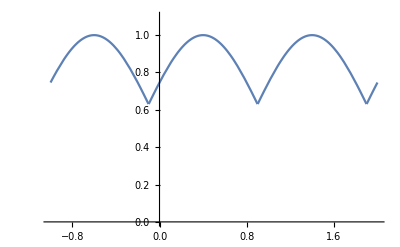

```mathematica
Plot[{g[x,g$pars={0.3,0.2}]},{x,-1,2},
ColorFunction->(Directive[Opacity[g[#1,g$pars]],rainbow[#2]]&),
ColorFunctionScaling->False,PlotRange->{0,1.1}]
Plot[{g[x,{0.4,3}]},{x,-1,2},
ColorFunctionScaling->False,PlotRange->{0,1.1}]
```

```mathematica
g[x,{0,1}]
```

#### Stuff

```mathematica
GaussianWindow
```

TODO -- figure out how to choose color based on where the poitn went in R^4.

Ways to pick 4 orthonormal vectors on 𝕊^3⊂ℝ^4
	After picking 2, the last 2-space can be chosen with one angle.
	Pick v1 in S^3 arbitrarily. Then there's a whole S^2 of choices for v2.
	After choosing those, there's only S^1 choices for v3 and then S^0 for v4.

#### Meshes

Strategy:
- Construct a cell structure on the domain D

- Attatch the mesh / cell structure to the actual data.

- Map it forward to T⊂ℝ^4 after choosing 3 radii.

- Project the data back down to ℝ^3 with some 4×3 projection matrix (choose 3 orthonormal vectors in ℝ^4)
	- would be super cool to have some inter-connected sliders that you can use to do interactive rotation in different ways in R^4.

#### Pictures

```mathematica
(* Visualize the domain D *)
MeshRegion[dm];
MeshRegion[dm,PlotTheme->"Lines",ImageSize->Medium];
```

```mathematica
MeshRegion[t3points,
Join[styfilter[0.4]/@dm2Cells,styfilter[1]/@dm1Cells],
RotationAction->"Clip",SphericalRegion->True]
```

-Graphics3D-

```mathematica
vf[pts_]:=Mod[Mean[pts.Normalize[{1,1,1}]],1]
MeshRegion[t3points,
Join[styfilter[1]/@dm1Cells],
RotationAction->"Clip",SphericalRegion->True]
```

-Graphics3D-

```mathematica
(* Transformation Matrix *)
tm=RandomVariate[CircularRealMatrixDistribution[4]]⟦All,1;;3⟧;
```

```mathematica
(* Here we go *)
tm0=;
id123=IdentityMatrix[{4,3}];
transformationMatrixToUse=id123; (* can be tm, tm0 or id123, any 4x3 matrix *)

radii=Normalize[{5,2,1}];
T=(torus/@t3points.radii);
MeshRegion[T.transformationMatrixToUse,
styfilter[1]/@dm1Cells,
MeshCellStyle->Directive[Thickness[0.003]],
RotationAction->"Clip",SphericalRegion->True]//Quiet
```

-Graphics3D-

```mathematica
MeshRegion[T.MatrixPower[tmat,3].id123,
styfilter[0.3]/@dm2Cells,
RotationAction->"Clip",SphericalRegion->True]//Quiet
```

-Graphics3D-

### An Example

```mathematica
(* configuration options *)
n=24;
s1=N@Subdivide[0,0.6,2n];
s2=N@Subdivide[0.6,1.3,n];
s3=N@Subdivide[0,1,n];
radii=Normalize[{5,4,1}];
vf[pts_]:=Mod[Mean[pts.Normalize[{1,0,-2}]],1];

tmat=RandomVariate[CircularRealMatrixDistribution[4]];
(*tmat=;*)

(* other stuff *)
pttable=Table[{x,y,z},{x,s1},{y,s2},{z,s3}];
t3points=Flatten[pttable,Depth[pttable]-3]; (* list of N points in R^3 *)
(*t3points=Select[t3points,x↦(Mod[Abs[x.Normalize[{1,1,2}]-0.3],1]<1)];*)

idx=ArrayReshape[Range[Length[t3points]],Most@Dimensions[pttable]];
getidx=Flatten[Array[List,Most[Dimensions[pttable]]],Depth[pttable]-3];

(* Set the mesh *)
dm=DelaunayMesh[t3points];
dmCells=MeshCells[dm,All];
dm1Cells=Select[MeshCells[dm,1],isAxisAligned];
dm2Cells=Select[MeshCells[dm,2],isAxisAligned];
(* Make the torus *)
T=(torus/@t3points.radii);
```

Here we're using the projection map P_t(x) = x . rotator[t] . id123
so the projection is dependant on t.
Future work includes finding other "cool" ways to define P_t(x).

```mathematica
Manipulate[
MeshRegion[(T.rotator[p1].id123)⟦All,1;;3⟧,
Join[
styfilter[{p2,0.5}]/@dm2Cells,
styfilter[1]/@dm1Cells],
RotationAction->"Clip",SphericalRegion->True
]//Quiet,
{{p1,0},0,6},
{{p2,0.185},0,1}
];
```

```mathematica
Manipulate[
MeshRegion[(T.rotator[p1])⟦All,1;;3⟧,
Join[
styfilter[{p3,1.5}]/@dm2Cells,
styfilter[0.5]/@dm1Cells],
MeshCellStyle->{0->None},
RotationAction->"Clip",SphericalRegion->True,
ImageSize->800,
Background->GrayLevel[0.15],
Axes->False,
AxesOrigin->{0,0,0},
AxesLabel->{x,y,z},
ViewPoint->{0, 0.7, 0}
]//Quiet,
{{p1,0.66*2π},0.001,2π},
{{p3,0.15},0,1}
];
```

Some snapshots of other settings:
-- be sure to set n to be a small number like 12 and run the code above before trying these examples.

```mathematica
DynamicModule[{p1=4.1468,p3=0.063},Quiet[MeshRegion[(T.rotator[p1])⟦All,1;;3⟧,Join[styfilter[{p3,1.5}]/@dm2Cells,styfilter[0.5]/@dm1Cells],MeshCellStyle->{0->None},RotationAction->"Clip",SphericalRegion->True,ImageSize->800,Background->GrayLevel[0.15],Axes->False,AxesOrigin->{0,0,0},AxesLabel->{x,y,z},ViewPoint->{0,0.7,0}]]];
```

```mathematica
DynamicModule[{p1=4.053009523130833,p3=0},Quiet[MeshRegion[(T.rotator[p1])⟦All,1;;3⟧,Join[styfilter[{p3,1}]/@dm2Cells,styfilter[1]/@dm1Cells],MeshCellStyle->{0->None},RotationAction->"Clip",SphericalRegion->True,ImageSize->Large,Background->GrayLevel[0.2],
Axes->True,AxesOrigin->{0,0,0},AxesLabel->{x,y,z},ViewPoint->{0,0.7,0}]]];
```

```mathematica
DynamicModule[{p1=2.0615567807549042,p3=0.298},Quiet[MeshRegion[(T.rotator[p1])⟦All,1;;3⟧,Join[styfilter[{p3,1}]/@dm2Cells,styfilter[1]/@dm1Cells],MeshCellStyle->{0->None},RotationAction->"Clip",SphericalRegion->True,ImageSize->Large,Background->GrayLevel[0.2],
Axes->True,AxesOrigin->{0,0,0},AxesLabel->{x,y,z},ViewPoint->{0,0.7,0}]]];
```

```mathematica
DynamicModule[{p1=2.1369430044410596,p3=1.},Quiet[MeshRegion[(T.rotator[p1])⟦All,1;;3⟧,Join[styfilter[{p3,1}]/@dm2Cells,styfilter[1]/@dm1Cells],MeshCellStyle->{0->None},RotationAction->"Clip",SphericalRegion->True,ImageSize->Large,Background->GrayLevel[0.2],
Axes->True,AxesOrigin->{0,0,0},AxesLabel->{x,y,z},ViewPoint->{0,0.7,0}]]];
```

```mathematica
MeshRegion[(T.tmat.rotator[π/2])⟦All,1;;3⟧,
Join[
(*styfilter[{0.185,0.5}]/@dm2Cells,*)
styfilter[{7.0/8,0.5}]/@dm1Cells],
RotationAction->"Clip",SphericalRegion->True
]
```

```mathematica
styfilter[{7.0/8,0.5}]/@dm1Cells
```

{}